HeatTransferModelAxisymmetric[T[r,z],{r,z},k,ρ,Cp,NoFlow,NoSource]

```mathematica
Remove["Global`*"]
pde=D[r*D[T[r],r],r]==-r
bcs={T[2]==300, (D[T[r],r]/.r->0.1)==-0.5};
T0a=300;
sola=NDSolve[{pde,bcs},T[r],{r,0.1,2}]
Plot[sola,{r,0.1,2}]
```

T'[r]+r T''[r]==-r

{{T[r]→InterpolatingFunction[…][r]}}

-Graphics-

```mathematica
-5+5 e
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

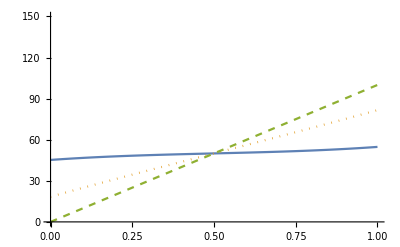

```mathematica
Remove["Global`*"]
pde=D[T[y,u],u]==D[D[T[y,u],y],y];
bcs={T[0,u]==0,T[1,u]==100,T[y,0]==T0};
T0a=50;
sola=NDSolve[{pde,bcs/.T0->T0a},T[y,u],{y,0,1},{u,0,10}];
tempS=T[y,u]/.sola/.u->0.1;
tempM=T[y,u]/.sola/.u->1;
tempL=T[y,u]/.sola/.u->10;
Plot[{tempS,tempM,tempL},{y,0,1},PlotStyle->{Solid,Dotted,Dashed},PlotRange->{0,150}]
70*^-6/1.6*^-19/(2*3.14*25*^-10)*Exp[-r*r/(2*25*^-10)]*2.4*^-13/0.9;
```